## Michael Dobbs Algorithmic Composition Program

```mathematica
ClearAll[transpose,retrograde,inversion,retrogradeinversion,palette,durationall,variation,v1,v2,beat,compiler,instruments,run]
```

## Palette of Variations

```mathematica
(*The following functions replicate compositional techniques that composers use to create music*)

(*
   m = pitch classes available to randomize, related to f of sound by: (p = 9 + 12 * Log[f / 440, 2])
tempo = integer (bpm)
*)

transpose[m_]:=(t:=Table[Table[m[[i]]+j,{i,1,Length[m]}],{j,1,11}];
PrependTo[t,m]); 
(*This double table function shows up in several of the following functions. It's function is to tranpose the motive into all twelve starting notes*)

(*
transpose[m_]:=With[{t=Table[Table[m[[i]]+j,{i,1,Length[m]}],{j,1,11}]},
Prepend[t,m]
]; 
*)

retrograde[m_]:=(r:=Reverse[m];
Retro:=Table[Table[r[[i]]+j,{i,1,Length[r]}],{j,1,11}];
PrependTo[Retro,r]); 
(*This function simply reverses the note order*)

inversion[m_]:=(
in:=Table[m[[i]]-m[[i+1]],{i,1,Length[m]-1}];
PrependTo[in,m[[1]]];
Inv:=Table[Table[in[[i]]+j,{i,1,Length[in]}],{j,1,11}];
PrependTo[Inv,in]);
(*This function inverts each indivual relationship between the note. For example: A,B will become A,G*)

retrogradeinversion[m_]:=(rt:=Reverse[(
inv2=Table[m[[i]]-m[[i+1]],{i,1,Length[m]-1}];
PrependTo[inv2,m[[1]]])];
RetroInv:=Table[Table[rt[[i]]+j,{i,1,Length[rt]}],{j,1,11}];
PrependTo[RetroInv,rt]);
(*This function reverses the inversion*)

palette[m_]:={transpose[m],retrograde[m],inversion[m],retrogradeinversion[m]};
(*This is the list of variations compiled from all the above functions*)
```

## Making Music

```mathematica
durationall[tempo_,m_(*,speed_*)]:=(60/tempo)*Length[m]*RandomChoice[{.05,.15,.25,.05,.35,.15,.05}->{4,2,1,2/3,1/2,1/3,1/4}];

(*Which[
speed==1,RandomChoice[{.12,.33,.55}->{4,2,1}],
speed==2,RandomChoice[{.38,.08,.54}->{1,2/3,1/2}],
speed==3,RandomChoice[{.64,.27,.09}->{1/2,1/3,1/4}],
speed==4,
]*)
(*Determines the note value and duration of each variation*)
(* attempting to implement notes to include (can use CheckBoxBar[Dynamic[notes],{key}]),
	or could change weights according to rule *)

variation[i_,tempo_,v_,m_,d_]:=Sound[
SoundNote[#,1,v]& /@palette[m][[RandomInteger[{1,4}]]][[RandomInteger[{1,12}]]],{i,i+d[tempo,m(*,speed*)]}
];
(*Selects one variation at random*)

(*Voice 1*)
v1[m_,voice_,tempo_,d_,l_]:=Sound[
Table[
If[
RandomChoice[{.2,.8}->{variation,rest}]==variation,
variation[i,tempo,voice,m,d],
Nothing,Nothing],
{i,0,l,(60/tempo)}]];
(*Randomly selects to play or to rest and then compiles all of the randomly selected variations into one output*)

(*Voice 2*)
v2[m_,voice2_,tempo_,d_,l_]:=Sound[
Table[
If[
RandomChoice[{.6,.4}->{variation,rest}]==variation,
variation[i,tempo,voice2,m,d],
Nothing,Nothing],
{i,0,l,(60/tempo)}]];
(*Randomly selects to play or to rest and then compiles all of the randomly selected variations into one output*)

compiler[m_,tempo_,l_,voice_,d1_,voice2_,d2_]:=Sound[{
Sound[v1[m,voice,tempo,d1,l],{0,QuantityMagnitude[Duration[v1[m,voice,tempo,d1,l]]]}],
Sound[v2[m,voice2,tempo,d2,l],{0,QuantityMagnitude[Duration[v2[m,voice2,tempo,d2,l]]]}]
}];
(*compiles the two voices together*)

(* NOT IMPLEMENTED YET *)

beat[tempo_]:=Sound[{Table[Sound[SoundNote["C",1,"Woodblock"],{i,i+1}],{i,0,30,(60/tempo)}]}];
(*Used for testing if the composition is following a beat*)
```

## Interface

```mathematica
instruments={"Accordion","AltoSax","Atmosphere","Bagpipe","BassAndLead","Bassoon","Bird","BlownBottle","Bowed","BrassSection","Brightness","Celesta","Cello","Choir","Clarinet","Dulcimer","ElectricGuitar","Fiddle","Fifths","Flute","FrenchHorn","Glockenspiel","Guitar","Harmonica","Harp","Harpsichord","Koto","Marimba","MusicBox","MutedTrumpet","Oboe","OrchestraHit","Organ","PanFlute","Piano","PizzicatoStrings","Recorder","Shamisen","Shanai","Sitar","Strings","TremoloStrings","Trumpet","TubularBells","Vibraphone","Viola","Violin","Voice","VoiceAahs","VoiceOohs","Warm","Whistle","Woodblock","Xylophone"};

run:=Panel[
DynamicModule[{m={0,2,6},tempo=100,voice2="Piano",voice1="Violin",l=30(*,speed=4*)},
Deploy[
Panel[
Grid[
Transpose[
{{"Pitch Class {}","Tempo (bpm)",(*"Speed of Notes",*)"Length (sec)","Voice 1","Voice 2",Space},
{InputField[Dynamic[m]],InputField[Dynamic[tempo]],(*SetterBar[Dynamic[speed],{1->"Slow",2->"Medium",3->"Fast",4->"All"}],*)InputField[Dynamic[l]],PopupMenu[Dynamic[voice1],instruments],PopupMenu[Dynamic[voice2],instruments],
Button["Generate",
{(* prints preset variables *)
Print[ToString[voice1]<>","<>ToString[voice2]<>", "<>ToString[tempo]<>"bmp, on "<>ToString[m]<>", for "<>ToString[l]<>"+s."],
(* "prints" music to be played *)
Print[compiler[m,tempo,l,voice1,durationall,voice2,durationall]]
}
]
}}
],
Alignment->Left
],Style["Algorithmic Composer",Italic,24],ImageMargins->10
]
]
]
]
```

```mathematica
run
```

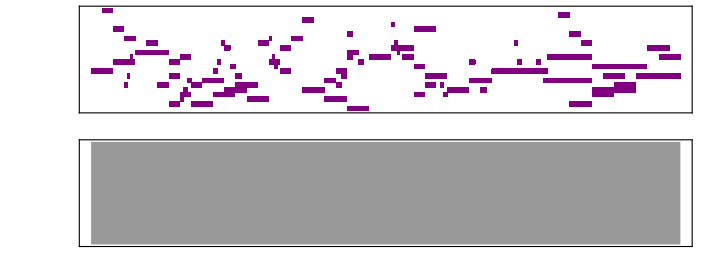

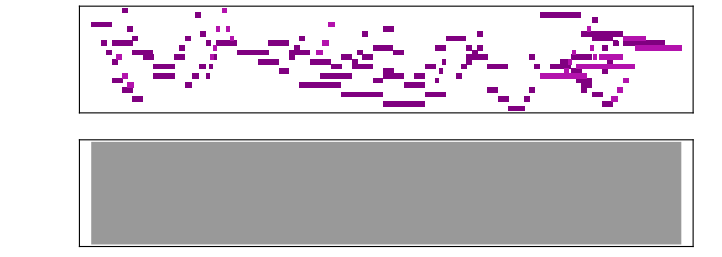

More ideas to implement:
Choose-
range of d,
SoundVolume -> v
multiple voices (overlayed: choose “density”, intensity of sounds; choose time-distribution of non-overlayed pieces to be sampled from)
	could make one the drums and overlay voice 1 throughout whole length
implement different scales option (pentatonic, jazz, blues, etc. - look up diff. scales on wiki)
Markov Chains for diff. types of notes (i.e. half notes after quarter notes)

Start with random notes and minimize objective function (which I would have to create)

look up chord structures, pair notes in chords such that they share nodes
implement chord progression formulae: http://www.lotusmusic.com/lm_chordprogressions.html



Start with base sound and randomize notes -

```mathematica
Audio[]
```

Audio::argt: Audio called with 0 arguments; 1 or 2 arguments are expected.

Audio[]

## Audio Lecture

Spectrogram[ ] to analyze, Cepstogram, periodogram

```mathematica
AudioJoin[]
```

AudioJoin::argx: AudioJoin called with 0 arguments; 1 argument is expected.

AudioJoin[]

```mathematica
AudioNormalize[]
```

AudioNormalize::argt: AudioNormalize called with 0 arguments; 1 or 2 arguments are expected.

AudioNormalize[]

## Meetings 28.6

SW:
primitive recursive functions, come from generative rule (substitution system (function in Math..), recursive function)
	note: underlying logic, but rich & complex
	enumerate rules, etc.
	create arbitrary nesting of primitives (append, double, )
	SW: as little randomness as possible

X:
define elementary actions (primitives) (shifting frequency, distortions (i.e. perturbations), etc.)
	define what they will be acting on

job: 	Find + create more elementary operations
	define function to take notes to other notes (can be deterministic or probabilistic) (referencing the beginning note of a crescendo, etc.)
	
long term: 	recognize patterns in music when rules are continually applied, create music based off these patterns, have fun and create some interesting music to show at presentation